The full algorithm to find a path to have the algorithm working.
TODO:  ad delta s and Delta p (for current position)

### Plotting the actual region (parametric form!)

```mathematica
(*This function makes the 2 step reachable set according to ψ*) 
makeRegionList[ψa_ , ps1_, ps2_]:= Module[{pra,γa,cola, regionlist},

(*ψa is  angle to the collision point *)
cola = 1/2{Cos[ ψa ],Sin[ψa ]}; (*collision point*)
pra= 2 Abs[ps1.cola-ps2.cola]; (*perpendicular distance*)
γa= ArcCos[1-2pra];(*reachable angle for other robot after first robot collides*)

regionlist = Polygon[Table[-cola+1/2{Cos[a],Sin[a]},{a,  ψa - γa ,ψa +γa,γa/20}]];
Return[regionlist]
]

calcαθ[ps1_,ps2_]:=(*call as {α,θ}=calcαθ[ps1,ps2]*)

Module[{d= Norm[ps1-ps2](*distance between robots*)},{ 2 ArcSin[d] (*angle between the two particles with respect to x-axis. This rotates the Δ-Config space*), ArcTan[ps1⟦1⟧-ps2⟦1⟧,ps1⟦2⟧-ps2⟦2⟧](*angular arc unreachable by robots in one move (there are two of these). Reachable set for first collision is 2π-2α.*)}]
(*This function calculates the minimum and maximum of ψ*)
calcψminmax [ps1_,ps2_]:= Module[{θ, α},
{α,θ}=calcαθ[ps1,ps2];
{θ+α/2-π/2,
θ-α/2+π/2}]
(*This functions calculates the γ, the angle between starting and ending point of the chord*)
calcγ[ψ_, ps1_,ps2_] := Module[{col, pra},
col = 1/2{Cos[ψ ],Sin[ψ ]};(*collision point for robot 2 -- where it hits the circular boundary*)
pra= 2 Abs[ps1.col-ps2.col]; (*perpendicular distance: maximum height of chord to boundary *)
Return[ArcCos[1-2pra]](*reachable angle for other robot after first robot collides*)]
(*This functions checks if a point p is in a chord that its center is c and has the ψ angle from the x axis, with γ length in a circle with raduis r*)
ifInChord[c_, ψ_, p_, γ_, r_]  := (
(*first test if inside the circle centered at c with radius r (we add a tiny amount to r because of machine precision -- Shva lost 6 hours of her short life for this)*)
If[(p⟦1⟧-c⟦1⟧)^2 + (p⟦2⟧-c⟦2⟧)^2> (r+0.0001)^2, Return [False]]; 
(*second test if in the half-plane defined by the chord from ψ-γ to ψ+γ, inclusive*)
 (c⟦1⟧-p⟦1⟧) Cos[ψ]+(c⟦2⟧-p⟦2⟧) Sin[ψ]≤ -r Cos[γ]+0.0001
)
(*This function find out if the point is inside the region*)
ifInRegion[ps1_,ps2_, nearest_, ψ_] := Module[{  γ,  c ,r= 1/2},
c= 1/2{Cos[ψ-π], Sin[ψ-π]}; (*Center of the circle that the chord is a part of*)
γ= calcγ[ψ,ps1,ps2];
If[ifInChord[c, ψ, Flatten@nearest, γ, r], Return[True] ,Return[False]];
]
(*This function finds the hit point angle *)
findHit[ps1_,ps2_, nearest_] := Module[(*This function finds the ψ of the chord when given two points on the cord. The points must be distinct*)
{  Δs (*beginning delta of the robots*)
, η (*The angle of the chord *)},
Δs = ps2 - ps1;
η = ArcTan[Δs⟦1⟧ - nearest⟦1⟧ , Δs⟦2⟧ - nearest⟦2⟧];
Return[η-π/2]
]
(*This function returns ψ*)
findPsi[ps1_,ps2_,nearest_] := Module[{ψ,ψmin,ψmax},
{ψmin, ψmax} = calcψminmax[ps1,ps2];
If[ ifInRegion[ps1,ps2, Flatten@nearest,ψmin],ψ=ψmin,
If[ifInRegion[ps1,ps2, Flatten@nearest, ψmax],ψ=ψmax,
ψ= findHit[ps1,ps2, Flatten@nearest];
If[ψ<ψmin, ψ+=2π];
If[ψ>ψmin+2π, ψ-=2π];
If[ψmin≤ψ≤ψmax,,ψ += π](*if ψ is not in the range of possible hit points, add π*)
]];

Return[ψ]
]
(*This function gives the whole 2-move reachable sets for a given starting positions of the particles*)
makeReachableSet[ps1_, ps2_] := Module[{ θ, α,ψa ,pra,γa,cola, γa2, polyline1, polyline2, polyline3, polyline4, finalpoly, reg},

{α,θ}=calcαθ[ps1,ps2];
cola = 1/2{Cos[ψa ],Sin[ψa ]}; (*collision point*)
pra= 2 Abs[ps1.cola-ps2.cola]; (*perpendicular distance*)
γa= ArcCos[1-2pra];(*reachable angle for other robot after first robot collides*)
γa2= ArcCos[1-2pra]/.{ψa-> θ+α/2+π/2};
polyline1 = Table[ 1/2{Cos[θ+α/2+π/2 ],Sin[θ+α/2+π/2 ]}-1/2{Cos[a2+θ+α/2+π/2],Sin[a2+θ+α/2+π/2]},{a2,0,+γa2,γa2/5}]; 
γa2= ArcCos[1-2pra]/.{ψa-> θ-α/2+3π/2};
polyline2 = Table[ 1/2{Cos[θ-α/2+3π/2 ],Sin[θ-α/2+3π/2 ]}-1/2{Cos[a2+θ-α/2+3π/2],Sin[a2+θ-α/2+3π/2]},{a2,-γa2,0,γa2/5}]; 
polyline3= Table[  1/2{Cos[ψa ],Sin[ψa ]}-1/2{Cos[ψa -γa],Sin[ψa -γa]},{ψa,θ+α/2+π/2,θ-α/2+3/2π,(π-α)/20}]; 
polyline4 = Table[  1/2{Cos[ψa ],Sin[ψa ]}-1/2{Cos[ψa +γa],Sin[ψa +γa]},{ψa,θ+α/2+π/2,θ-α/2+3/2π,(π-α)/20}]; 

finalpoly = Join[polyline2,polyline1, polyline4, polyline3];
finalpoly= DeleteDuplicates[Round[finalpoly,1/100000]];
reg = Polygon[finalpoly];

Return[reg]
]

(*Adds one step to moves*)
stepToGoal[ps1_,ps2_,pe1_,pe2_, moves_, pm1_,pm2_]:=Module[{reg, nearest, Δg, ψ, r1, r2, Δr, path, path1, path2
},
Δg = pe2-pe1;
path = moves;
path1 = pm1;
path2= pm2;
reg = makeReachableSet[ps1,ps2];
nearest = RegionNearest[reg,Flatten@Δg];

(*We always consider the blue robot(second robot) hit the wall first. This is why we always subtract pi from psi, and subtract ps2 from delta r*)
ψ= findPsi[ps1,ps2,Flatten@nearest]- π;
If[Abs[Flatten@nearest - Flatten@ Δg]>0.001,ψ= ψ-π/4];
Δr = 1/2{Cos[ψ],Sin[ψ]}-ps2;

AppendTo[path, Δr];
r1 = ps1+ Δr;
AppendTo[path1, r1];
r2 = ps2 + Δr;
AppendTo[path2, r2];
Δr= -Flatten@nearest +r2-r1;
AppendTo[path, Δr];
r1 = r1+ Δr;
AppendTo[path1, r1];
(*r2 = ps2 + Δr;*)
AppendTo[path2, r2];
Return[{path, path1, path2, r1, r2}]
]
(*Returns the required moves for a given starting and goal positions*)
pathToGoal[ps1_,ps2_,pe1_,pe2_]:=Module[{moves, pm1, pm2, r1, r2},

{moves, pm1, pm2, r1, r2}= stepToGoal[ps1, ps2, pe1, pe2, {{0,0}}, {ps1}, {ps2}];
While[  Abs[Norm[pe2-pe1] - Norm[r2-r1]]>0.001 ,
{moves, pm1, pm2, r1, r2}= stepToGoal[r1, r2, pe1, pe2, moves,pm1, pm2];
];
AppendTo[moves, pe1-r1];
AppendTo[pm1,pe1];
AppendTo[pm2,pe2];
Return[{moves, pm1, pm2}]
]
distanceMoved[moves_,num_]:= Total[Table[Norm[m],{m,moves[[1;;num]]}]]
distanceMoved2[moves_]:= Total[Table[Norm[m],{m,moves}]]

clipCircle[p_,ϵ_]:=If[Norm[p]>1/2-ϵ,(1/2-ϵ)p/Norm[p],p]; (*keeps robots inside of circle of radius 1/2-ϵ*)
ϵ = 1/1000;
```

```mathematica
Manipulate[Module[{thickness = 0.002,
θ(*angle between the two particles*),
α(*anglular arc unreachable by robots*),
r = 1/40 (*radius of start and end markers*),
writingHeight = 0.8,
(*left robot*) ps1,pe1,
(*right robot*) ps2,pe2,
(*collision point*)pcol1,
pm1, pm2,mvNum,
mvFrac,
path, path1, path2,
Δg ,
ψmin, ψmax, dist, 
c1=Blue,c2 =Red},

s1=clipCircle[s1,ϵ];
e1=clipCircle[e1,ϵ];
s2=clipCircle[s2,ϵ];
e2=clipCircle[e2,ϵ];
Δg = {pe2-pe1};

{ps1 ,pe1,ps2,pe2} = {s1,e1,s2,e2};
{α,θ}=calcαθ[ps1,ps2];
{path,path1,path2} = pathToGoal[ps2,ps1,pe2,pe1];

mvNum = Floor[progress*(Length[path]-1)] ;
dist = distanceMoved[path, mvNum+1];
mvFrac = FractionalPart[progress*(Length[path]-1)];
pm2= If[mvFrac>0,path2⟦mvNum+1,;;⟧+mvFrac*(path2⟦mvNum+2,;;⟧-path2⟦mvNum+1,;;⟧),path2⟦mvNum+1,;;⟧];
pm1 = If[mvFrac>0,path1⟦mvNum+1,;;⟧+mvFrac*(path1⟦mvNum+2,;;⟧-path1⟦mvNum+1,;;⟧),path1⟦mvNum+1,;;⟧];
If[mvFrac>0,dist = dist+ Norm[mvFrac*(path⟦mvNum+2,;;⟧-path⟦mvNum+1,;;⟧)]];
If[progress == 1, mvNum = Length[path]-2];
Graphics[{
(*workspace*)
{Darker[Red], Disk[{0,0},1.05/2]},
{Lighter[Gray,0.8], Disk[{0,0},1/2]},
{White, Disk[{0,0},1/2-ϵ]},
{Lighter[Gray,0.8], Disk[ps2,ϵ]},
PointSize[0.01],
Arrowheads[.03],

(*plot path of particle 1*)
{c2,
Table[Arrow[{path1⟦i,;;⟧,path1⟦i+1,;;⟧}],{i,1,mvNum}],
 Arrow[{path1⟦mvNum+1,;;⟧,pm1}],
{If[pm1⟦1⟧==0||pm1⟦2⟧==0||pm1⟦1⟧==1||pm1⟦2⟧==1,{Point@pm1 ,PointSize[0.005],White,Point@pm1 },Point@pm1] }
},


(*plot path of particle 2*)
 {c1,
Table[Arrow[{path2⟦i,;;⟧,path2⟦i+1,;;⟧}],{i,1,mvNum}],
 Arrow[{path2⟦mvNum+1,;;⟧,pm2}],
{If[pm2⟦1⟧==0||pm2⟦2⟧==0||pm2⟦1⟧==1||pm2⟦2⟧==1,{Point@pm2 ,PointSize[0.005],White,Point@pm2 },Point@pm2]}
},
Text[Style[StringForm["workspace"],Black,FontSize->38,FontFamily-> "Times"],{0,-0.65}],
Text[Style[StringForm["Δ configuration space"],Black,FontSize->38,FontFamily-> "Times"],{1.75,-0.65}],
Text[Style[StringForm["Current"],Black,FontSize->38,FontFamily-> "Times"],{-0.3,writingHeight+0.2}],
Text[Style[StringForm["Goal"],Black,FontSize->38,FontFamily-> "Times"],{-0.3,writingHeight}],
Text[Style[StringForm["Move `` of ``", mvNum+1, Length[path]-1],Black,FontSize->38,FontFamily-> "Times"],{0.25,writingHeight+0.5}],
Text[Style[StringForm["Distance `` of `` ", SetPrecision[dist,3],SetPrecision[distanceMoved[path(*,mvNum*)],3]],FontSize->38,FontFamily-> "Times"],{0.27,writingHeight+0.7}],
{c1,Thickness[thickness],EdgeForm[Directive[c1,Thickness[thickness]]],FaceForm[None],Rectangle[{0.32,writingHeight+0.18},{0.36,writingHeight+0.22}],Circle[{0.33,writingHeight},r]},
{c2,Thickness[thickness],EdgeForm[Directive[c2,Thickness[thickness]]],FaceForm[None],Rectangle[{0.16,writingHeight+0.18},{0.2,writingHeight+0.22}], Circle[{0.17,writingHeight},r]},
Text[Style[StringForm["="],Black,FontSize->38,FontFamily-> "Times"],{0.09,writingHeight+0.2}],
Text[Style[StringForm["-"],Black,FontSize->38,FontFamily-> "Times"],{0.25,writingHeight+0.2}],
Text[Style[StringForm["="],Black,FontSize->38,FontFamily-> "Times"],{0.09,writingHeight}],
Text[Style[StringForm["-"],Black,FontSize->38,FontFamily-> "Times"],{0.25,writingHeight}],

Darker[Green], Rectangle[{0,writingHeight+0.18},{0.04,writingHeight+0.22}], Green, Disk[{0.01,writingHeight},r],

(*starting poses, dashed line from start to end*)
{c1,Thickness[thickness],{ Opacity[.3],Dashed,Arrow[{ps1,pe1}]},Point@ps1,EdgeForm[Directive[c1,Thickness[thickness]]],FaceForm[None],Rectangle[ps1-2/3r {1,1},ps1+2/3r{1,1}],Circle[pe1,r]},
{c2,Thickness[thickness],{ Opacity[.3],Dashed,Arrow[{ps2,pe2}]},Point@ps2,EdgeForm[Directive[c2,Thickness[thickness]]],FaceForm[None],Rectangle[ps2-2/3r {1,1},ps2+2/3r{1,1}], Circle[pe2,r]},

Inset[Module[{ regionlist, ψ},
(*ParametricPlot[a,{a,-0.1,0.1},(*{cola-1/2{Cos[a],Sin[a]}}, {ψa,θ+α/2+π/2,θ-α/2+3/2π},{a,ψa -γa ,ψa +γa},*)PlotRange-> {{-1,1},{-1,1}},*)
Graphics[FrameLabel->{"Δx","Δ y"},LabelStyle->Directive[Black,18],ImageSize->500, Epilog-> {Circle[{0,0},1-2ϵ],

reg = makeReachableSet[pm2,pm1];
nearest = RegionNearest[reg,Δg];
ψ= findPsi[pm2,pm1,Flatten@nearest];
regionlist = makeRegionList[ψ, pm2, pm1];

{Blue,Opacity[0.5],EdgeForm[Black], reg},(*{Red,Opacity[0.1],EdgeForm[Directive[Red]],regionlist},*)
(*current deltas*)
Darker[Green],Rectangle[pm1-pm2-4/3r {1,1},pm1-pm2+4/3r{1,1}],Text[Style[StringForm["Δs"],Italic, FontSize->38,Black,FontFamily-> "Times"],{pm1⟦1⟧-pm2⟦1⟧+ 0.1,pm1⟦2⟧-pm2⟦2⟧+0.1}],
Green, Disk[Flatten@Δg,r], (*Red, Disk[Flatten@nearest, r],*)Text[Style[StringForm["Δg"],Italic,Black,FontSize->38,FontFamily-> "Times"],pe2-pe1-{.1,.1}]}]],{1.8,0.5}]
},ImageSize->810,PlotRange->{{-0.55,3},{-0.75,1.75}}]],


Row[{Control@{{progress,1,"progress"},0,1,1/420,Slider,Appearance->"Label
ed"},
Control@{{ϵ,1/1000,"ϵ"},1/1000,1/5,1/1000,Slider,Appearance->"Labeled"}}],
{{s1,{0.0,0.0}},{-1/2,-1/2}+ ϵ,{1/2,1/2}- ϵ,Locator,Appearance->None},
{{s2,{0.2,0.4}},{-1/2,-1/2}+ ϵ,{1/2,1/2}- ϵ,Locator,Appearance->None},
{{e1,{0.05,0.35}},{-1/2,-1/2}+ ϵ,{1/2,1/2}- ϵ,Locator,Appearance->None},
{{e2,{-0.33,0.26}},{-1/2,-1/2}+ ϵ,{1/2,1/2}- ϵ,Locator,Appearance->None}
, SaveDefinitions->True]
```

## Make Smooth Animations

### InitializeCode

```mathematica
frameCirc[progress_,ϵ_,s1i_,s2i_,e1i_,e2i_]:=Module[{thickness = 0.002,
θ(*angle between the two particles*),
α(*anglular arc unreachable by robots*),
r = 1/40 (*radius of start and end markers*),
ftsz = 72,
writingHeight = 0.8,
(*left robot*) ps1,pe1,
(*right robot*) ps2,pe2,
(*collision point*)pcol1,
pm1, pm2,mvNum,
mvFrac,
path, path1, path2,
Δg ,
ψmin, ψmax, dist, 
s1,s2,e1,e2,
c1=Blue,c2 =Red},

s1=clipCircle[s1i,ϵ];
e1=clipCircle[e1i,ϵ];
s2=clipCircle[s2i,ϵ];
e2=clipCircle[e2i,ϵ];
Δg = {pe2-pe1};

{ps1 ,pe1,ps2,pe2} = {s1,e1,s2,e2};
{α,θ}=calcαθ[ps1,ps2];
{path,path1,path2} = pathToGoal[ps2,ps1,pe2,pe1];

mvNum = Floor[progress*(Length[path]-1)] ;
dist = distanceMoved[path, mvNum+1];
mvFrac = FractionalPart[progress*(Length[path]-1)];
pm2= If[mvFrac>0,path2⟦mvNum+1,;;⟧+mvFrac*(path2⟦mvNum+2,;;⟧-path2⟦mvNum+1,;;⟧),path2⟦mvNum+1,;;⟧];
pm1 = If[mvFrac>0,path1⟦mvNum+1,;;⟧+mvFrac*(path1⟦mvNum+2,;;⟧-path1⟦mvNum+1,;;⟧),path1⟦mvNum+1,;;⟧];
If[mvFrac>0,dist = dist+ Norm[mvFrac*(path⟦mvNum+2,;;⟧-path⟦mvNum+1,;;⟧)]];
If[progress == 1, mvNum = Length[path]-2];
Graphics[{
(*workspace*)
{Darker[Red], Disk[{0,0},1.05/2]},
{Lighter[Gray,0.8], Disk[{0,0},1/2]},
{White, Disk[{0,0},1/2-ϵ]},
{Lighter[Gray,0.8], Disk[ps2,ϵ]},
PointSize[0.01],
Arrowheads[.03],

(*plot path of particle 1*)
{c2,
Table[Arrow[{path1⟦i,;;⟧,path1⟦i+1,;;⟧}],{i,1,mvNum}],
 Arrow[{path1⟦mvNum+1,;;⟧,pm1}],
{If[pm1⟦1⟧==0||pm1⟦2⟧==0||pm1⟦1⟧==1||pm1⟦2⟧==1,{Point@pm1 ,PointSize[0.005],White,Point@pm1 },Point@pm1] }
},


(*plot path of particle 2*)
 {c1,
Table[Arrow[{path2⟦i,;;⟧,path2⟦i+1,;;⟧}],{i,1,mvNum}],
 Arrow[{path2⟦mvNum+1,;;⟧,pm2}],
{If[pm2⟦1⟧==0||pm2⟦2⟧==0||pm2⟦1⟧==1||pm2⟦2⟧==1,{Point@pm2 ,PointSize[0.005],White,Point@pm2 },Point@pm2]}
},
Text[Style[StringForm["workspace"],Black,FontSize->ftsz,FontFamily-> "Times"],{0,-0.65}],
Text[Style[StringForm["Δ configuration space"],Black,FontSize->ftsz,FontFamily-> "Times"],{1.75,-0.65}],
Text[Style[StringForm["Current"],Black,FontSize->ftsz,FontFamily-> "Times"],{-0.3,writingHeight+0.2}],
Text[Style[StringForm["Goal"],Black,FontSize->ftsz,FontFamily-> "Times"],{-0.3,writingHeight}],
Text[Style[StringForm["Move `` of ``", mvNum+1, Length[path]-1],Black,FontSize->ftsz,FontFamily-> "Times"],{0.25,writingHeight+0.5}],
Text[Style[StringForm["Distance `` of `` ", SetPrecision[dist,3],SetPrecision[distanceMoved2[path(*,mvNum*)],3]],FontSize->ftsz,FontFamily-> "Times"],{0.27,writingHeight+0.7}],
{c1,Thickness[thickness],EdgeForm[Directive[c1,Thickness[thickness]]],FaceForm[None],Rectangle[{0.32,writingHeight+0.18},{0.36,writingHeight+0.22}],Circle[{0.33,writingHeight},r]},
{c2,Thickness[thickness],EdgeForm[Directive[c2,Thickness[thickness]]],FaceForm[None],Rectangle[{0.16,writingHeight+0.18},{0.2,writingHeight+0.22}], Circle[{0.17,writingHeight},r]},
Text[Style[StringForm["="],Black,FontSize-> ftsz,FontFamily-> "Times"],{0.09,writingHeight+0.2}],
Text[Style[StringForm["-"],Black,FontSize->ftsz,FontFamily-> "Times"],{0.25,writingHeight+0.2}],
Text[Style[StringForm["="],Black,FontSize->ftsz,FontFamily-> "Times"],{0.09,writingHeight}],
Text[Style[StringForm["-"],Black,FontSize->ftsz,FontFamily-> "Times"],{0.25,writingHeight}],

Darker[Green], Rectangle[{0,writingHeight+0.18},{0.04,writingHeight+0.22}], Green, Disk[{0.01,writingHeight},r],

(*starting poses, dashed line from start to end*)
{c1,Thickness[thickness],{ Opacity[.3],Dashed,Arrow[{ps1,pe1}]},Point@ps1,EdgeForm[Directive[c1,Thickness[thickness]]],FaceForm[None],Rectangle[ps1-2/3r {1,1},ps1+2/3r{1,1}],Circle[pe1,r]},
{c2,Thickness[thickness],{ Opacity[.3],Dashed,Arrow[{ps2,pe2}]},Point@ps2,EdgeForm[Directive[c2,Thickness[thickness]]],FaceForm[None],Rectangle[ps2-2/3r {1,1},ps2+2/3r{1,1}], Circle[pe2,r]},

Inset[Module[{ regionlist, ψ},
(*ParametricPlot[a,{a,-0.1,0.1},(*{cola-1/2{Cos[a],Sin[a]}}, {ψa,θ+α/2+π/2,θ-α/2+3/2π},{a,ψa -γa ,ψa +γa},*)PlotRange-> {{-1,1},{-1,1}},*)
Graphics[FrameLabel->{"Δx","Δ y"},LabelStyle->Directive[Black,18],ImageSize->950, Epilog-> {Thickness[0.005],Circle[{0,0},1-2ϵ],

reg = makeReachableSet[pm2,pm1];
nearest = RegionNearest[reg,Δg];
ψ= findPsi[pm2,pm1,Flatten@nearest];
regionlist = makeRegionList[ψ, pm2, pm1];

{Blue,Opacity[0.5],EdgeForm[Black], reg},(*{Red,Opacity[0.1],EdgeForm[Directive[Red]],regionlist},*)
(*current deltas*)
Darker[Green],Rectangle[pm1-pm2-4/3r {1,1},pm1-pm2+4/3r{1,1}],Text[Style[StringForm["Δs"],Italic, FontSize->ftsz,Black,FontFamily-> "Times"],{pm1⟦1⟧-pm2⟦1⟧+ 0.1,pm1⟦2⟧-pm2⟦2⟧+0.1}],
Green, Disk[Flatten@Δg,r], (*Red, Disk[Flatten@nearest, r],*)Text[Style[StringForm["Δg"],Italic,Black,FontSize->ftsz,FontFamily-> "Times"],pe2-pe1-{.1,.1}]}]],{1.8,0.5}]
},ImageSize->{1920,1080},(*ImageSize->{1920,1080},*)PlotRange->{{-0.55,3},{-0.75,1.75}}]]
```

### Make video

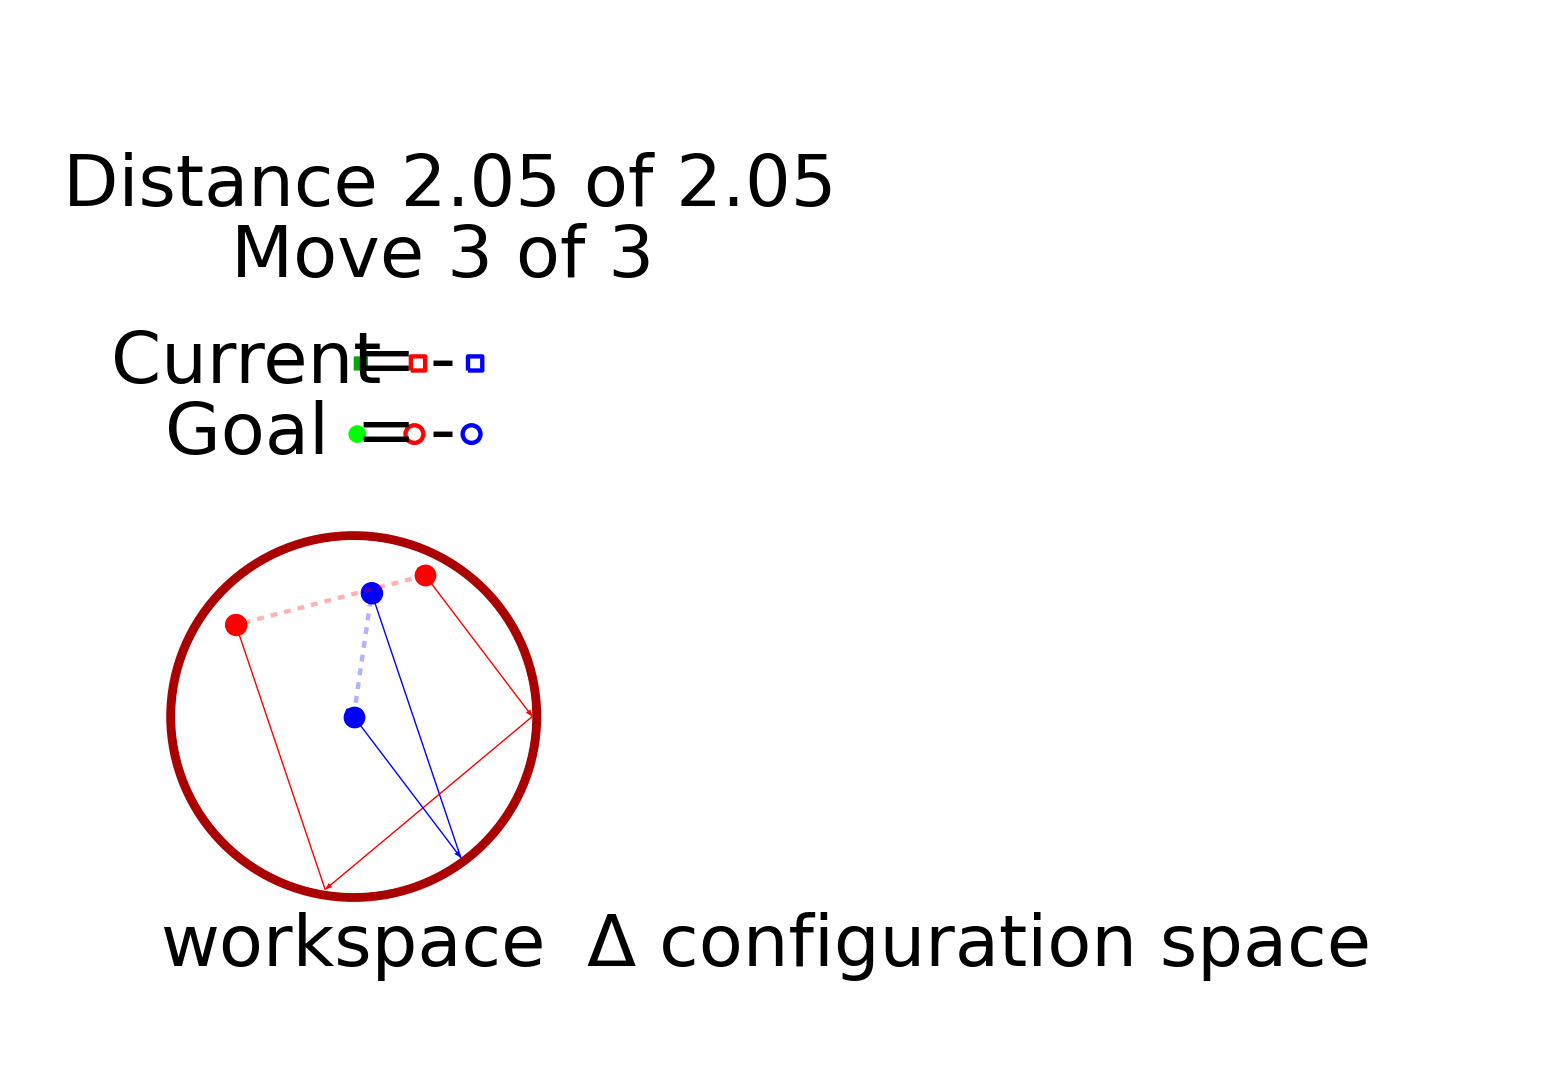
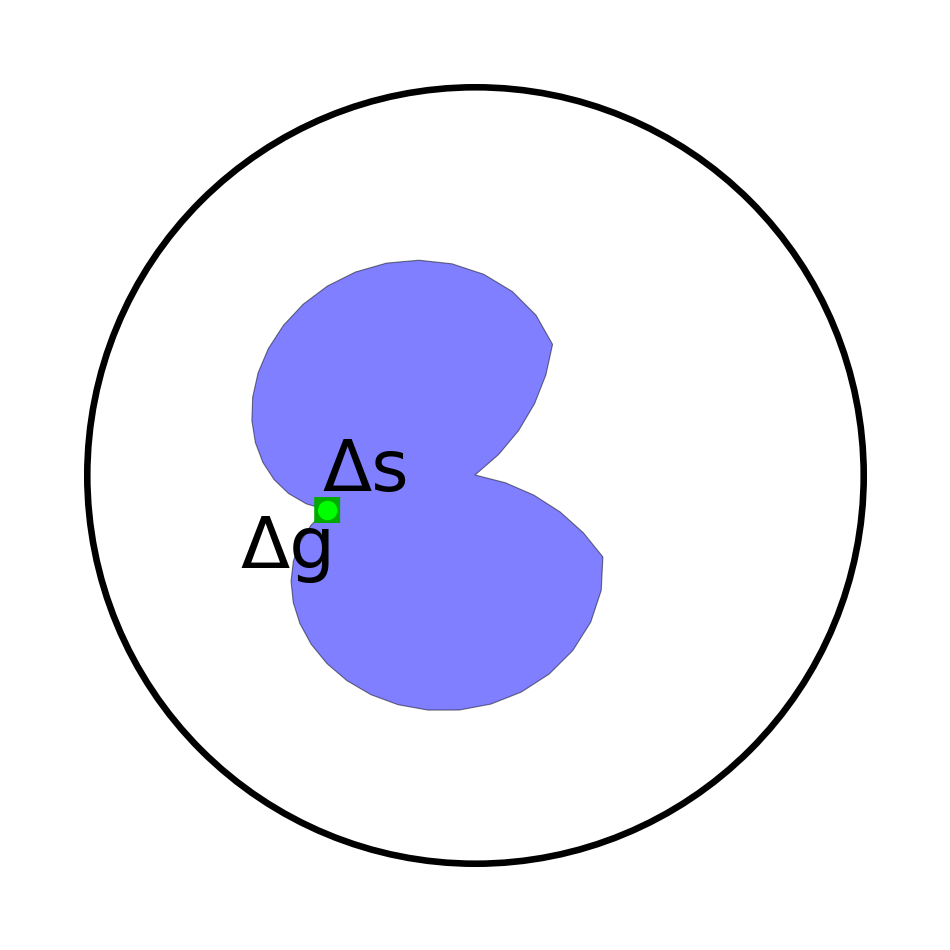

```mathematica
(*s1={0.0,0.0};s2={0.2,0.4};e1={0.05,0.35};e2={-0.33,0.26};
frameCirc[0.02,1/1000,s1,s2,e1,e2]*)
frameCirc[1,1/1000,{0.0,0.0},{0.2,0.4},{0.05,0.35},{-0.33,0.26}]
```

```mathematica
(*Step 1: generate a table of frames*)
frameCircs=ParallelTable[frameCirc[t,1/1000,{0.0,0.0},{0.2,0.4},{0.05,0.35},{-0.33,0.26}],{t,0,1,1/300}];

(*frameCircs=ParallelTable[Piecewise[{
{frameHex[e1,0,False,False],t<1},
{frameHex[(t-1)/3(e2-e1)+e1,0,False,False],t<4},
{frameHex[e2,(t-4)/4,False,False],t<8},
{frameHex[-(t-8)/3(e2-e1)+e2,1,False,False],t<11},


{frameHex[(t-11)/3(e2-e1)+e1,1,True,True],t<14},
{frameHex[e2,1-(t-14)/4,True,True],t<18},
{frameHex[-(t-18)/3(e2-e1)+e2,0,True,True],t<21},
{frameHex[e1,0,True,True],t<22}}

],{t,0,21,1/15}];*)
```

```mathematica
(*step 2: export frames as video*)
Export["diskCircs.avi",frameCircs];
```

```mathematica
frameCircs2=ParallelTable[frameCirc[0,1/1000,{t,0.0},{0.2,0.4},{0.05,0.35},{-0.33,0.26}],{t,-1,0,1/300}];
Export["diskCircs2.avi",frameCircs];
```